```mathematica
Clear["Global`*"]
```

```mathematica
n=5
```

5

```mathematica
ν=n 0.001/Pi//N
tf=1
```

0.00159155

1

```mathematica
EqBurgers=-D[u[t,x],t]-u[t,x]D[u[t,x],x]+ν D[u[t,x],x,x]==0
```

-u[t,x] u^(0,1)[t,x]+0.00159155 u^(0,2)[t,x]-u^(1,0)[t,x]==0

```mathematica
CondICC={u[0,x]==-Sin[Pi x],u[t,-1]==0,u[t,1]==0}
```

{u[0,x]==-Sin[π x],u[t,-1]==0,u[t,1]==0}

```mathematica
sol=NDSolve[{EqBurgers,CondICC},u,{x,-1,1},{t,0,tf}, MaxStepSize->0.0002]//Timing
```

{28.5313,{{u→InterpolatingFunction[{{0., 1.}, {-1., 1.}}, <>]}}}

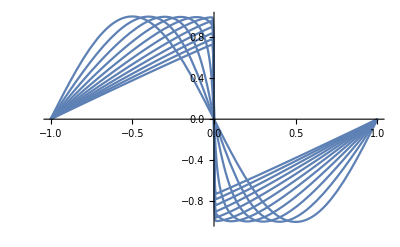

```mathematica
Plot[Table[u[i,x]/.sol[[2]],{i,0,tf,0.1}],{x,-1,1}]
```

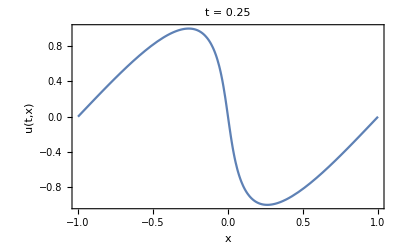

```mathematica
t025=Plot[Table[u[i,x]/.sol[[2]],{i,0.24,0.26}],{x,-1,1},PlotLabel->"t = 0.25",PlotRange->{{-1,1},{-1,1}},Frame->True,FrameLabel->{"x","u(t,x)" }]
```

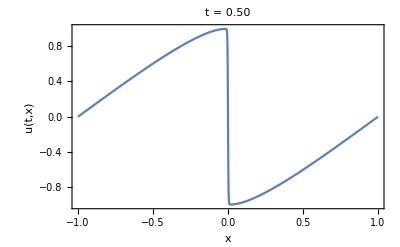

```mathematica
t050=Plot[Table[u[i,x]/.sol[[2]],{i,0.49,0.51}],{x,-1,1},PlotLabel->"t = 0.50",PlotRange->{{-1,1},{-1,1}},Frame->True,FrameLabel->{"x","u(t,x)" }]
```

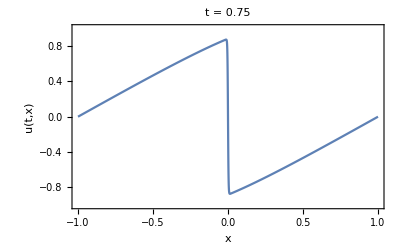

```mathematica
t075=Plot[Table[u[i,x]/.sol[[2]],{i,0.74,0.76}],{x,-1,1},PlotLabel->"t = 0.75",PlotRange->{{-1,1},{-1,1}},Frame->True,FrameLabel->{"x","u(t,x)" }]
```

```mathematica
p1=DensityPlot[Evaluate[u[t,x]/.sol[[2]]],{t,0,tf},{x,-1,1},PlotRange->{-1.5,1.5},PlotLabel->"u(t,x)",AspectRatio->1/3,ImageSize->Large,FrameLabel->Automatic,ColorFunction->"Rainbow",PlotLegends->Placed[Automatic,After],PlotPoints->300,MaxRecursion->3]
```

-Graphics-

```mathematica
p2=Plot3D[Evaluate[u[t,x]/.sol[[2]]],{t,0,tf},{x,-1,1},PlotRange->{-1.5,1.5},ColorFunction->"Rainbow",PlotLegends->Automatic,PlotLabel->"u(t,x)",AxesLabel->Automatic,PlotPoints->300, MaxRecursion->3,ViewPoint->{-3.500300993084546,0.8810897685460463,0.985684420884688}]
```

-Graphics3D-

```mathematica
α[t_,x_]:=u[t,x]/.Flatten[sol[[2]]]
α[0,0]
```

-5.42101×10^-20

```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\Academy and Work\UNIFEI - Universidade Federal de Itajubá\TFG - Machine Learning N-S\BURGERS - CONT-IDENT\0 - PRINCIPAL\Conjunto 1\extra - un5

```mathematica
Export["un1_t025.png",t025, ImageResolution->200]
```

un1_t025.png

```mathematica
Export["un1_t050.png",t050,ImageResolution->200]
```

un1_t050.png

```mathematica
Export["un1_t075.png",t075,ImageResolution->200]
```

un1_t075.png

```mathematica
Export["un1_burgers_math.png",p1, ImageResolution->200]
```

un1_burgers_math.png

```mathematica
Export["un1_3d.png",p2,ImageResolution->200]
```

un1_3d.png

```mathematica
Export["usol.dat",Table[α[t,x],{x,-1,1,N[tf/255]},{t,0,1,0.01}]]
Export["x.dat",Table[x,{x,-1,1,N[tf/255]}]]
Export["t.dat",Table[t,{t,0,1,0.01}]]
```

usol.dat

x.dat

t.dat